```mathematica
elementList={"Sc"->1,"Ti"->2,"V"->3,"Cr"->4,"Mn"->5,"Fe"->6,"Co"->7,"Ni"->8,"Cu"->9,"Zn"->10,"Y"->11,"Zr"->12,"Nb"->13,"Mo"->14,"Tc"->15,"Ru"->16,"Rh"->17,"Pd"->18,"Ag"->19,"Hf"->20,"Ta"->21,"W"->22,"Re"->23,"Os"->24,"Ir"->25,"Pt"->26,"Au"->27};
elements=List@@@elementList//Transpose//First;
targets = {ORR -> -1.51, CORedCO -> -1.20, ORedCO -> -1.25};
```

## Parse Data:

```mathematica
data=Import["/home/marco/fridbDemo/allresults.json"];
```

Parse 38 atom NP oxygen binding energy:

```mathematica
atoms32=Select[data,StringCases[#[[1]],"32"]≠{}&];
atoms32Binding=Select[atoms32,StringCases[#[[1]],"Binding"]≠{}&];
dataall={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms32Binding)/.elementList;
tab=Table[Cases[dataall,{m,n,_}][[;;,3]],{m,1,27},{n,1,27}]//MatrixForm;
smallBindingTable = Table[With[{x=Cases[dataall,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];
Table[With[{x=Cases[dataall,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}]//MatrixForm;
```

Parse 79 atom NP oxygen:

```mathematica
atoms79=Select[data,StringCases[#[[1]],"60"]≠{}&];
atoms79Binding=Select[atoms79,StringCases[#[[1]],"Binding"]≠{}&];
dataall79={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms79Binding)/.elementList;
tab=Table[Cases[dataall79,{m,n,_}][[;;,3]],{m,1,27},{n,1,27}]//MatrixForm;
bigBindingTable = Table[With[{x=Cases[dataall79,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];
Table[With[{x=Cases[dataall,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}]//MatrixForm;
```

## Make Matrix Plots:

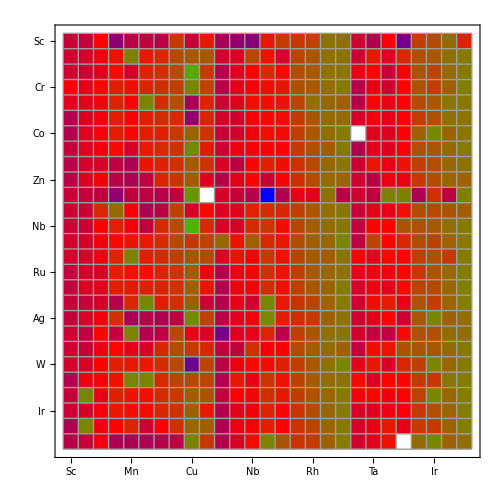

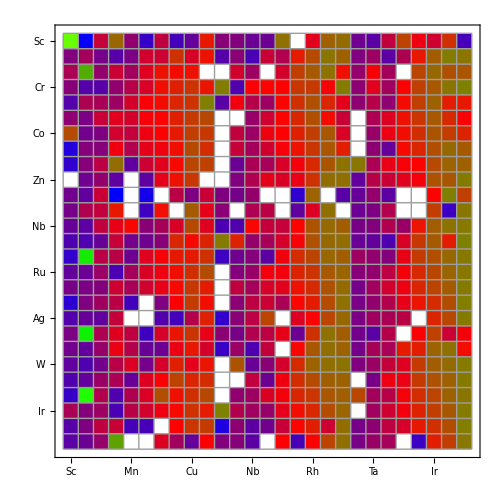

```mathematica
MatrixPlot[smallBindingTable,ColorFunction->(Blend[{Blue,Red, Green, Yellow},#]&),ColorRules->{0->White},Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]

MatrixPlot[bigBindingTable,ColorFunction->(Blend[{Blue,Red, Green, Yellow},#]&),ColorRules->{0->White},Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]
```

## Make Bar Charts:

### These statements are used to filter out spurious binding energies. Then nanoparticle removed has its corresponding label removed, so that the bar chart bars and their labes line up correctly

{{12}}

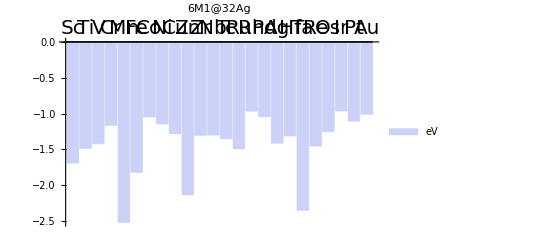

{{Sc},{Ti},{V},{Cr},{Mn},{Fe},{Co},{Ni},{Cu},{Zn},{Y},{Zr},{Nb},{Mo},{Tc},{Ru},{Rh},{Pd},{Ag},{Hf},{Ta},{W},{Re},{Os},{Ir},{Pt},{Au}}

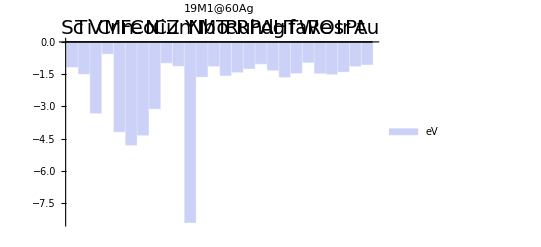

{{Sc},{Ti},{V},{Cr},{Mn},{Fe},{Co},{Ni},{Cu},{Zn},{Y},{Zr},{Nb},{Mo},{Tc},{Ru},{Rh},{Pd},{Ag},{Hf},{Ta},{W},{Re},{Os},{Ir},{Pt},{Au}}

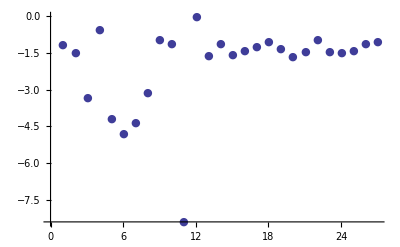

-Graphics-

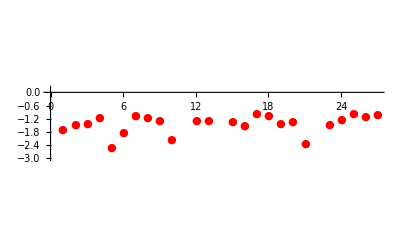

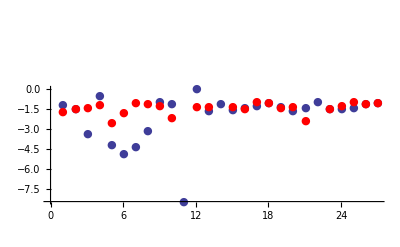

{0.528839,0.00008181,-1.8915,0.6229,-1.66226,-2.97975,-3.29121,-1.96083,0.313333,1.02347,1.6646,1.30394,-0.314616,-5.48928,-0.205317,0.0908144,-0.267932,0.0252885,0.100085,-0.317968,0.904503,-5.36616,0.00134848,-0.242626,-0.417037,-0.0155537,-0.0349103}

```mathematica
placeholder =DeleteCases[Map[ If[# >0 || # <-10 ,0,#] &,smallBindingTable[[All,19]] ],0];
removedElementsPos = Position[Map[ If[# >0 || # <-10 ,0,#] &,smallBindingTable[[All,19]] ],0];
newElementsSmall = Delete[elements, # & /@removedElementsPos] ;

placeholder2 =DeleteCases[Map[ If[# >0 || # <-10 ,0,#] &,bigBindingTable[[All,19]] ],0];
removedElementsPos2 = Position[Map[ If[# >0 || # <-10,0,#] &,bigBindingTable[[All,19]] ],0]
newElementsBig = Delete[elements, # & /@removedElementsPos2] ;
newElementsSmall == newElementsBig;
Delete[placeholder2, 1] ;

BarChart[placeholder,ChartLabels->{Placed[Style[#,FontSize->20]&/@newElementsSmall,Above]},PlotLabel->Style["6M1@32Ag",Bold,50],ChartLegends->{"eV"}]
{#} & @@{#, Medium } & /@  elements

BarChart[placeholder2,ChartLabels->{Placed[Style[#,FontSize->20]&/@newElementsBig,Above]},PlotLabel->Style["19M1@60Ag",Bold,50],ChartLegends->{"eV"}]
{#} & @@{#, Medium } & /@  elements
p1 = ListPlot[{#} & @bigBindingTable[[All,19]], FillingStyle-> Thick, PlotMarkers -> {Automatic, Medium}]


Show[p1,Graphics[{Red,elements}] ]
p2 = ListPlot[smallBindingTable[[All,19]], FillingStyle-> Thick, PlotMarkers -> {Automatic, Medium}, PlotStyle -> Red]
Show[p1,p2]
bigBindingTable[[All, 19]] - smallBindingTable[[All,19]]
```

## Ag, Pt Dot Chart

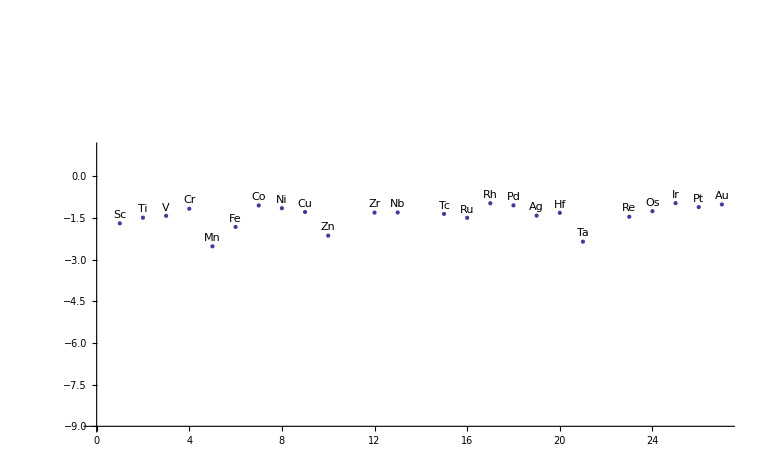

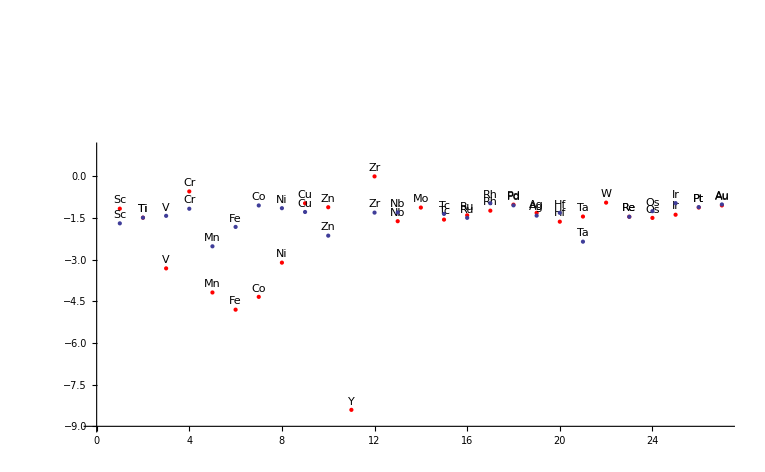

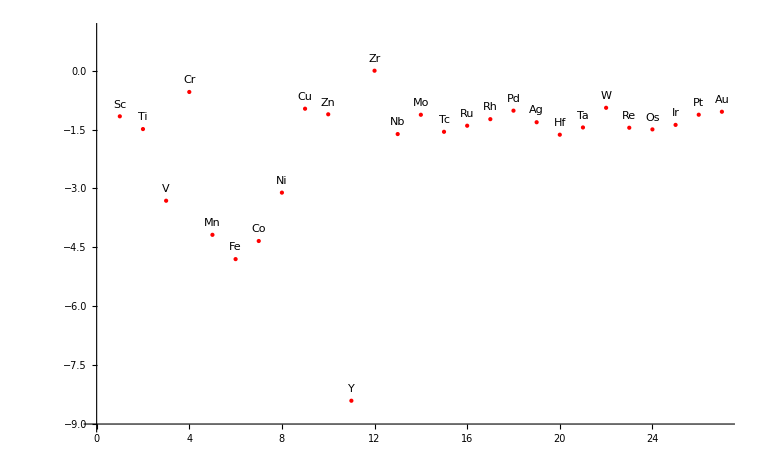

-Graphics-

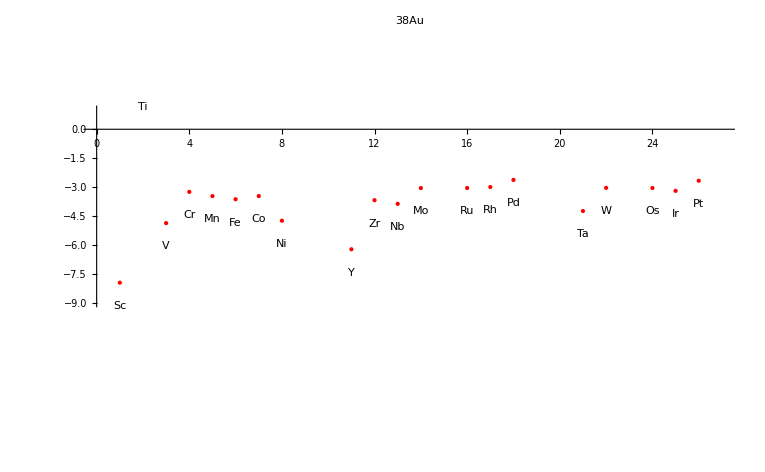

```mathematica
dataPlot1=ListPlot[smallBindingTable[[All,19]],PlotStyle->PointSize->Large,AxesOrigin->{0,-9},PlotRange->{Automatic,{-9,1}}];
labels1=MapThread[Text[#1,{#2,#3+0.3}]&,{elements,Range[Length@smallBindingTable[[All,19]]],smallBindingTable[[All,19]]}];
Show[dataPlot1,Graphics[labels1]]

dataPlot2=ListPlot[bigBindingTable[[All,19]],PlotStyle->{Red,PointSize->Large},AxesOrigin->{0,-9},PlotRange->{Automatic,{-9,1}}];
labels2=MapThread[Text[#1,{#2,#3+0.3}]&,{elements,Range[Length@bigBindingTable[[All,19]]],bigBindingTable[[All,19]]}];

dataPlot3=ListPlot[smallBindingTable[[All,27]] - ORR /. targets,PlotStyle->{Red,PointSize->Large},PlotRange->{Automatic,{-9,1}},PlotLabel -> "38Au", AxesOrigin->{0,0} ];
labels3=MapThread[Text[#1,{#2,#3+0.3}]&,{elements,Range[Length@smallBindingTable[[All,27]]],smallBindingTable[[All,5]]}];





































Show[dataPlot2,Graphics[labels2], dataPlot1, Graphics[labels1]]
Show[dataPlot2,Graphics[labels2]]
Show[dataPlot1, Graphics[labels1]]
Show[dataPlot3,Graphics[labels3]]
```

```mathematica
lst = Delete[lst,3]
```

Delete::partw: Part {3} of lst does not exist.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

Delete::partw: Part {3} of Delete[Delete[Hold[Delete[lst, 3]], 3], 3] does not exist.

Delete::partw: Part {3} of Delete[Delete[Delete[Hold[Delete[lst, 3]], 3], 3], 3] does not exist.

Delete::partw: Part {3} of Delete[Delete[Delete[Delete[Hold[Delete[lst, 3]], 3], 3], 3], 3] does not exist.

General::stop: Further output of Delete :: partw will be suppressed during this calculation.

Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[Delete[MaxFormatDepthExceededMaxFormatDepthExceededMaxFormatDepthExceeded],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3],3]

## Average Bond Length Plots:

```mathematica
bondLenData = Import["/home/marco/fridbDemo/avgbondlen.json"] /. elementList;
```

Get Bond Length for bnp 38 nanoparticles

```mathematica
lst=  "bnp" /. bondLenData[[1]];
lst = "38" /. lst;

lst = Delete[lst,3];
lst = Delete[lst,8];
bnp38BL = Table[x, {x,1,27}] /. lst;
```

Get Bond Length for bnp 79 nanoparticles:

```mathematica
lst2=  "bnp" /. bondLenData[[1]];
lst2 = "79" /. lst2;
lst2 = Delete[lst,3];
lst2 = Delete[lst,8];
bnp79BL = Table[x, {x,1,27}] /. lst2; 

bondLenData[[1]]
```

bnp→{38→{19→2.85077,27→2.8549,Cd→2.88438,7→2.8297,4→2.84034,9→2.81286,6→2.8282,20→2.96446,Hg→2.87532,25→2.83727,5→2.83799,14→2.84114,13→2.91995,8→2.83038,24→2.84655,18→2.84554,26→2.84533,23→2.86048,17→2.84004,16→2.84042,1→2.92212,21→2.91318,15→2.85081,2→2.88824,3→2.87623,22→2.89723,11→2.96313,10→2.84196,12→2.97649},79→{19→2.87259,27→2.87463,Cd→2.88172,7→2.78466,4→2.82841,9→2.80938,6→2.77798,20→3.00874,25→2.81191,5→2.80125,14→2.82716,13→2.83941,8→2.7879,24→2.79815,18→2.82765,26→2.83002,23→2.8378,17→2.81816,16→2.80325,1→2.9742,21→2.96703,15→2.82528,2→2.8858,3→2.80727,22→2.83959,11→2.96012,10→2.85065}}

Make Plots of Bond Length data:

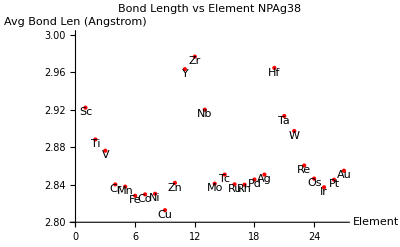

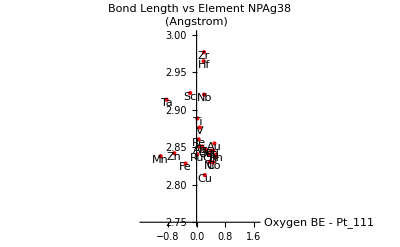

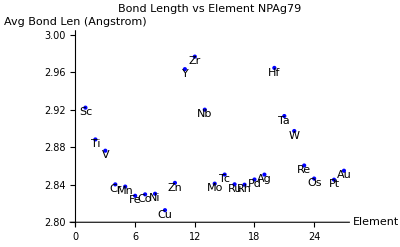

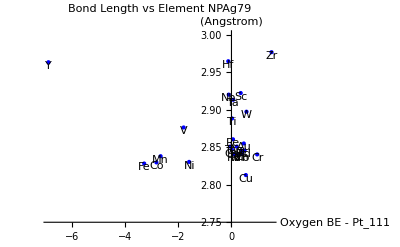

```mathematica
bondLenVsElement38 = ListPlot[bnp38BL, PlotStyle -> {Red, PointSize -> Large},PlotRange -> {2.80, 3},  PlotLabel -> "Bond Length vs Element NPAg38", AxesLabel->{"Element", "Avg Bond Len (Angstrom)"}];
bondLenVsElementLabels38=MapThread[Text[#1,{#2,#3-0.005}]&,{elements,Range[Length@bnp38BL], bnp38BL}];

bondLenVsBe38data = Partition[#,2] & @Riffle[#1, #2] & @@{smallBindingTable[[All,19]] - ORR /. targets, bnp38BL};
bondLenVsBe38=ListPlot[bondLenVsBe38data, PlotStyle->{Red,PointSize->Large}, PlotRange->{2.75, 3}, PlotLabel -> "Bond Length vs Element NPAg38", AxesLabel->{"Oxygen BE - Pt_111", "(Angstrom)"}];
bondLenVsBeLabels38=MapThread[Text[#1,{#2 ,#3- 0.005}]&,{elements,smallBindingTable[[All,19]] - ORR /. targets, bnp38BL}];

bondLenVsElement79 = ListPlot[bnp79BL, PlotStyle -> {Blue, PointSize -> Large},PlotRange -> {2.80, 3},  PlotLabel -> "Bond Length vs Element NPAg79", AxesLabel->{"Element", "Avg Bond Len (Angstrom)"}];
bondLenVsElementLabels79=MapThread[Text[#1,{#2,#3-0.005}]&,{elements,Range[Length@bnp79BL], bnp79BL}];

bondLenVsBe79data = Partition[#,2] & @Riffle[#1, #2] & @@{bigBindingTable[[All,19]] - ORR /. targets, bnp79BL};
bondLenVsBe79=ListPlot[bondLenVsBe79data, PlotStyle->{Blue,PointSize->Large}, PlotRange->{2.75, 3}, PlotLabel -> "Bond Length vs Element NPAg79", AxesLabel->{"Oxygen BE - Pt_111", "(Angstrom)"}];
bondLenVsBeLabels79=MapThread[Text[#1,{#2 ,#3- 0.005}]&,{elements,bigBindingTable[[All,19]] - ORR /. targets, bnp79BL}];




Show[bondLenVsElement38, Graphics[bondLenVsElementLabels38] ]
Show[bondLenVsBe38, Graphics[bondLenVsBeLabels38] ]

Show[bondLenVsElement79, Graphics[bondLenVsElementLabels79] ]
Show[bondLenVsBe79, Graphics[bondLenVsBeLabels79] ]
```

## Filter Particles:

```mathematica
idealORRSmall = Replace[smallBindingTable- (ORR) /. targets,a_/;Abs[a]≥0.05->0,{2}] ;
idealORRBig = Replace[bigBindingTable- (ORR) /. targets ,a_/;Abs[a] ≥0.05->0,{2}];


info[tbl_]:=With[{s=SparseArray[tbl]},ArrayPad[Append@@@Transpose[{s["NonzeroPositions"],s["NonzeroValues"]}],{0,{1,0}},ToString@Unevaluated@tbl]]

SetAttributes[info,HoldFirst]


DeleteCases[  info[idealORRSmall]/.  Reverse /@ elementList,{__,"no"}]
DeleteCases[  info[idealORRBig]/.  Reverse /@ elementList,{__,"no"}]
```

{{idealORRSmall,Sc,Pd,0.0381286},{idealORRSmall,Ti,Ag,0.0234839},{idealORRSmall,Mn,Rh,-0.0418618},{idealORRSmall,Fe,Pt,-0.0379584},{idealORRSmall,Cu,Au,-0.00495028},{idealORRSmall,Ru,Ag,0.0179224},{idealORRSmall,W,Pd,-0.0176639}}

{{idealORRBig,Sc,Pd,-0.00103932},{idealORRBig,Ti,Ag,0.0235657},{idealORRBig,Mn,Ir,0.0309183},{idealORRBig,Cu,Au,0.0284615},{idealORRBig,Tc,Ag,-0.046035},{idealORRBig,Re,Pd,-0.0441911},{idealORRBig,Re,Pt,0.0172549},{idealORRBig,Os,Ag,0.015038},{idealORRBig,Os,Pt,0.0314884}}

### Filter For Tunable Particles:

```mathematica
returnValueTest[row_, col_,tbl_] := tbl[[row,col]] 
tables = { smallBindingTable, bigBindingTable};

(* get diagonal elements.  A particle is tunable if its pure form is on the opposite side of the volcano from its core@shell partner.  Assume The list we are operating on has had the target binding energy subtracted from every entry in the table.  Then two particles are on opposite sides of the volcano if one has a positive energy and the other has a negative energy.  Here we search the diagnol (which corresponds to a pure particle). At each diagonal step we search the column.  If any element in the column is opposite in sign from any core elements (the column) then the particle is tunable.*)

(*filterTunable[tbls_, rxnTarget_]:= Function[myTable,{
tunableORRData=Replace[myTable,a_/;Abs[a]≥10->0,{2}]- (-1.51)/.targets; (*set any spurious values to zero *)
(* A particle is tunable if its pure form (located on the diagnols of the table) is opposite in sign to its core@shell parnter *)
d=Sign@Diagonal@tunableORRData;
returnValue[row_,col_,myTable]:=myTable[[row,col]];
tunablePairs=Position[(tunableORRDataᵀ d)ᵀ,_?Negative]/.Reverse/@elementList;
pairEnergy=returnValue[#1,#2]&@@{#1,#2}&@@@Position[(tunableORRDataᵀ d)ᵀ,_?Negative];
tempVar=Partition[Riffle[tunablePairs,pairEnergy],2];
filterImposs=Replace[tempVar,a_/;Abs[a]≥5->0,{2}];
filterImposs=Replace[filterImposs,a_/;a>1->0,{2}];
Cases[filterImposs,{x_,y_}/;y≠0]}][#, ORR]&/@tbls ;

getPure[position_]:= position[[2]]

preProcTunable[tbls_, binTbl_]:= Function[myTable,{
tst =  smallBindingTable[[#,#]] & /@ Flatten[{ getPure[#1] }& @@@myTable[[1]] /. elementList];
 MapThread[Append,{myTable[[1]],tst}]}][#] & /@ tbls

idealRatio[EbCoreShell_ ,EbPt111_,EbPure_]:= (EbCoreShell - EbPt111)/(EbCoreShell - EbPure) 

{small, big } = preProcTunable[{#1, #2} & @@ filterTunable[tables]];


impossFilter1 = Replace[ratioList,a_/;Abs[a]≥1->"no",{1}];
impossFilter2 = Replace[impossFilter1,a_/;a <0->"no",{1}];

combineFilter = ArrayFlatten[{{big[[1]],Transpose[{impossFilter2}]}}];

DeleteCases[combineFilter,{__,"no"}]

ratioList = idealRatio[small[[1, All, 2]], -1.51, small[[1,All,3]]];
impossFilter1 = Replace[ratioList,a_/;Abs[a]≥1->"no",{1}];
impossFilter2 = Replace[impossFilter1,a_/;a <0->"no",{1}];

combineFilter = ArrayFlatten[{{small[[1]],Transpose[{impossFilter2}]}}];

DeleteCases[combineFilter,{__,"no"}]; *)
```

#### Filter Small Particles:

```mathematica
returnValue[row_,col_,myTable_]:=myTable[[row,col]];
idealRatio[EbCoreShell_ ,EbPt111_,EbPure_]:= (EbCoreShell - EbPt111)/(EbCoreShell - EbPure) 

filter =Replace[smallBindingTable,a_/;Abs[a]≥10->"no",{2}]- (-1.51)/.targets; (*set any spurious values to zero *)
(* A particle is tunable if its pure form (located on the diagnols of the table) is opposite in sign to its core@shell parnter *)

d=Sign@Diagonal@filter;

tunablePairs=Position[(filterᵀ d)ᵀ,_?Negative]/.Reverse/@elementList;
pairEnergy=returnValue[#1,#2, smallBindingTable]&@@{#1,#2}&@@@Position[(filterᵀ d)ᵀ,_?Negative];
tempVar=Partition[Riffle[tunablePairs,pairEnergy],2];
filterImposs=Replace[tempVar,a_/;Abs[a]≥5->"no",{2}];
filterImposs=Replace[filterImposs,a_/;a>1->"no",{2}];
filterImposs = DeleteCases[filterImposs,{__,"no"}];

Cases[filterImposs,{x_,y_}/;x[[2]]≠("Zn")];
Cases[%,{x_,y_}/;x[[2]]≠("Zr")];
Partition[Riffle[ %[[All,1]],%[[All,2]] - (-1.5)],2];
tunableSmall = DeleteCases[%,{x_,y_}/;y==1.5]

tunableSmall[[All,1,2]]
pure = Extract[bigBindingTable, Partition[Riffle[ tunableSmall[[All,1,2]] /. Reverse /@ elementList, tunableSmall[[All,1,2]] /. Reverse /@ elementList],2]];

ratioList = idealRatio[ tunableSmall[[1,All,2]], -1.51, tunableSmall[[1,All,3]]];

tunableSmall =  ArrayFlatten[{{tunableSmall,Transpose[{pure}]}}];

tunableSmall


finalTunableSmall/.{{l1_,l2_},x1_,x2_,_}:>Thread@Tooltip[Thread@{l2/.elementList,{x1,x2}},{l1,l2}]

ListPlot[Union@@%,PlotStyle->PointSize[Large],PlotRangePadding->2, PlotRange->{Automatic}]






(*smallBindingTable[[#,#]] & /@ tstlst*)
```

{{{Sc,Pd},0.0281286},{{Sc,Ag},-0.190714},{{Ti,Mn},2.36011},{{Ti,Au},0.307046},{{V,Au},0.394868},{{Cr,Au},1.36829},{{Mn,Ag},-1.01796},{{Mn,Pt},0.204625},{{Mn,Au},0.281574},{{Fe,Ag},-0.319391},{{Fe,Au},0.0591171},{{Co,Au},0.196051},{{Ni,Au},0.828044},{{Zn,Ag},-0.633972},{{Y,W},1.31071},{{Nb,Au},0.413001},{{Mo,Au},0.323605},{{Tc,Au},0.577362},{{Ru,Au},0.712045},{{Rh,Au},1.0173},{{Pd,Au},1.12087},{{Ta,Ag},-0.8501},{{Ta,Au},0.379714},{{W,Au},0.338647},{{Re,Pt},0.27026},{{Re,Au},0.454877},{{Os,Au},0.73896},{{Ir,Au},0.921008},{{Pt,Au},0.906137}}

{Pd,Ag,Mn,Au,Au,Au,Ag,Pt,Au,Ag,Au,Au,Au,Ag,W,Au,Au,Au,Au,Au,Au,Ag,Au,Au,Pt,Au,Au,Au,Au}

Extract::psl: Position specification {{"Pd", "Pd"}, {"Ag", "Ag"}, {"Mn", "Mn"}, {"Au", "Au"}, {"Au", "Au"}, {"Au", "Au"}, {"Ag", "Ag"}, {"Pt", "Pt"}, {"Au", "Au"}, {"Ag", "Ag"}, {"Au", "Au"}, {"Au", "Au"}, {"Au", "Au"}, {"Ag", "Ag"}, {"W", "W"}, {"Au", "Au"}, {"Au", "Au"}, {"Au", "Au"}, {"Au", "Au"}, {"Au", "Au"}, {"Au", "Au"}, {"Ag", "Ag"}, {"Au", "Au"}, {"Au", "Au"}, {"Pt", "Pt"}, {"Au", "Au"}, {"Au", "Au"}, {"Au", "Au"}, {"Au", "Au"}} in Extract[{« 1 »}, {{"Pd", "Pd"}, {"Ag", "Ag"}, {"Mn", "Mn"}, {"Au", "Au"}, {"Au", "Au"}, {"Au", "Au"}, {"Ag", "Ag"}, {"Pt", "Pt"}, {"Au", "Au"}, {"Ag", "Ag"}, {"Au", "Au"}, {"Au", "Au"}, {"Au", "Au"}, {"Ag", "Ag"}, {"W", "W"}, {"Au", "Au"}, {"Au", "Au"}, {"Au", "Au"}, {"Au", "Au"}, {"Au", "Au"}, {"Au", "Au"}, {"Ag", "Ag"}, {"Au", "Au"}, {"Au", "Au"}, {"Pt", "Pt"}, {"Au", "Au"}, {"Au", "Au"}, {"Au", "Au"}, {"Au", "Au"}}] is not a machine-sized integer or a list of machine-sized integers.

Part::partd: Part specification {{{"Sc", "Pd"}, 0.0281286}, {{"Sc", "Ag"}, -0.190714}, {{"Ti", "Mn"}, 2.36011}, {{"Ti", "Au"}, 0.307046}, {{"V", "Au"}, 0.394868}, {{"Cr", "Au"}, 1.36829}, {{"Mn", "Ag"}, -1.01796}, {{"Mn", "Pt"}, 0.204625}, « 14 », {{"Ta", "Au"}, 0.379714}, {{"W", "Au"}, 0.338647}, {{"Re", "Pt"}, 0.27026}, {{"Re", "Au"}, 0.454877}, {{"Os", "Au"}, 0.73896}, {{"Ir", "Au"}, 0.921008}, {{"Pt", "Au"}, 0.906137}} ⟦ 1, All, 2 ⟧ is longer than depth of object.

Part::partw: Part 3 of {"Sc", "Pd"} does not exist.

Transpose::nmtx: The first two levels of the one-dimensional list {Extract[{{156.593, -52.0823, -4.8808, -1.38635, -5.99529, -20.0851, -5.10796, -13.6342, -7.31414, -3.21067, -6.26199, -6.32499, -6.99733, -6.96793, -1.04173, 0, -4.19145, -1.51104, -1.16187, -6.84807, -8.31656, -5.06085, -2.33724, -4.02743, -4.54608, -2.71657, -13.4038}, {« 1 »}, « 23 », {« 1 »}, {-8.11528, -6.96224, -5.8536, 21.348, 0, 0, « 15 », -5.57802, 0, -17.8416, -3.11806, -2.45439, -0.786697}}, {« 1 »}]} cannot be transposed.

{«1»,«27»,{{Pt,Au},«11»,Transpose[{Extract[{{156.593,-52.0823,-4.8808,-1.38635,-5.99529,-20.0851,-5.10796,-13.6342,-7.31414,-3.21067,-6.26199,-6.32499,-6.99733,-6.96793,-1.04173,0,-4.19145,-1.51104,-1.16187,-6.84807,-8.31656,-5.06085,-2.33724,-4.02743,-4.54608,-2.71657,-13.4038},«26»},{{Pd,Pd},{Ag,Ag},{Mn,Mn},{Au,Au},«21»,{Au,Au},{Au,Au},{Au,Au},{Au,Au}}]}]}}

{{{Sc,Pd},0.0281286,-0.708094},{{Sc,Ag},-0.190714,0.0972691},{{Ti,Mn},2.36011,-3.46377},{{Ti,Au},0.307046,-0.184442},{{V,Au},0.394868,-0.184442},{{Cr,Au},1.36829,-0.184442},{{Mn,Ag},-1.01796,0.0972691},{{Mn,Pt},0.204625,-0.741024},{{Mn,Au},0.281574,-0.184442},{{Fe,Ag},-0.319391,0.0972691},{{Fe,Au},0.0591171,-0.184442},{{Co,Au},0.196051,-0.184442},{{Ni,Au},0.828044,-0.184442},{{Zn,Ag},-0.633972,0.0972691},{{Y,W},1.31071,-4.60537},{{Nb,Au},0.413001,-0.184442},{{Mo,Au},0.323605,-0.184442},{{Tc,Au},0.577362,-0.184442},{{Ru,Au},0.712045,-0.184442},{{Rh,Au},1.0173,-0.184442},{{Pd,Au},1.12087,-0.184442},{{Ta,Ag},-0.8501,0.0972691},{{Ta,Au},0.379714,-0.184442},{{W,Au},0.338647,-0.184442},{{Re,Pt},0.27026,-0.741024},{{Re,Au},0.454877,-0.184442},{{Os,Au},0.73896,-0.184442},{{Ir,Au},0.921008,-0.184442},{{Pt,Au},0.906137,-0.184442}}

ListPlot::lpn: {-4.60537, -3.46377, -1.01796, -0.8501, -0.741024, -0.708094, -0.633972, -0.319391, -0.190714, -0.184442, 0.0281286, 0.0591171, 0.0972691, 0.196051, 0.204625, 0.27026, « 19 », {"Co", "Au"}, {"Cr", "Au"}, {"Fe", "Ag"}, {"Fe", "Au"}, {"Ir", "Au"}, {"Mn", "Ag"}, {"Mn", "Au"}, {"Mn", "Pt"}, {"Mo", "Au"}, {"Nb", "Au"}, {"Ni", "Au"}, {"Os", "Au"}, {"Pd", "Au"}, {"Pt", "Au"}, {"Re", "Au"}, « 14 »} is not a list of numbers or pairs of numbers.

ListPlot[{-4.60537,-3.46377,-1.01796,-0.8501,-0.741024,-0.708094,-0.633972,-0.319391,-0.190714,-0.184442,0.0281286,0.0591171,0.0972691,0.196051,0.204625,0.27026,0.281574,0.307046,0.323605,0.338647,0.379714,0.394868,0.413001,0.454877,0.577362,0.712045,0.73896,0.828044,0.906137,0.921008,1.0173,1.12087,1.31071,1.36829,2.36011,{Co,Au},{Cr,Au},{Fe,Ag},{Fe,Au},{Ir,Au},{Mn,Ag},{Mn,Au},{Mn,Pt},{Mo,Au},{Nb,Au},{Ni,Au},{Os,Au},{Pd,Au},{Pt,Au},{Re,Au},{Re,Pt},{Rh,Au},{Ru,Au},{Sc,Ag},{Sc,Pd},{Ta,Ag},{Ta,Au},{Tc,Au},{Ti,Au},{Ti,Mn},{V,Au},{W,Au},{Y,W},{Zn,Ag}},PlotStyle→PointSize[Large],PlotRangePadding→2,PlotRange→{Automatic}]

#### Filter Large:

```mathematica
returnValue[row_,col_,myTable_]:=myTable[[row,col]];
filter =Replace[bigBindingTable,a_/;Abs[a]≥10->666,{2}]- (-1.51)/.targets; (*set any spurious values to zero *)
(* A particle is tunable if its pure form (located on the diagnols of the table) is opposite in sign to its core@shell parnter *)




d=Sign@Diagonal@filter;

tunablePairs=Position[(filterᵀ d)ᵀ,_?Negative]/.Reverse/@elementList;
pairEnergy=returnValue[#1,#2, bigBindingTable]&@@{#1,#2}&@@@Position[(filterᵀ d)ᵀ,_?Negative];
tempVar=Partition[Riffle[tunablePairs,pairEnergy],2];
filterImposs=Replace[tempVar,a_/;Abs[a]>5->666,{2}];

Cases[filterImposs,{x_,y_}/;x[[2]]≠("Zn")];
Cases[%,{x_,y_}/;x[[2]]≠("Zr")];
Partition[Riffle[ %[[All,1]],%[[All,2]] ],2];
tunableBig = DeleteCases[%,{x_,y_}/;y==0];


 DeleteDuplicates[ Flatten[ tunableBig[[All,1]] ] ];

pure = Extract[ bigBindingTable, Partition[Riffle[ tunableBig[[All,1,2]] /. elementList , tunableBig[[All,1,2]] /. elementList],2]];

(*ratio = idealRatio[finalTunableBig[[All,2]], -1.51, finalTunableBig[[All,3]] ]; *)
tunableBig = ArrayFlatten[{{tunableBig,Transpose[{pure}]}}];

ratio = (tunableBig[[All,2]] + 1.51)/(tunableBig[[All,2]] - tunableBig[[All,3]]);



finalTunableBig= ArrayFlatten[{{tunableBig,Transpose[{ratio}]}}];

finalTunableBig = DeleteCases[finalTunableBig,{x_,y_,z_,f_}/;z==666];
finalTunableBig = DeleteCases[finalTunableBig,{x_,y_,z_,f_}/;y==666]





finalTunableadj = {#1,#2+1.51,#3+1.51, #4 } &@@@finalTunableBig[[All,1;;]];

finalTunableadj/. {{l1_,l2_},x1_ ,x2_ ,_}:>Thread@Labeled[Thread@{l2/.elementList,{x1,x2}},{l1,l2}];

SortBy[ finalTunableadj /. elementList,#[[2]]&] /. Reverse /@ elementList;

tst = ListPlot[Udfnion@@%,Evaluate[PlotRange->{{1,27}, {-1,1}}],PlotStyle->PointSize[Large],Ticks->({#}&@Transpose@{Range@Length@elements,elements})];
```

#### Format Data Table for export:

```mathematica
core = PrependTo[finalTunableadj[[All,1,1]], "  "];
finaltunableadja
```

{  ,{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y},{  ,Cr,Tc,Pd,Pt,Pd,Ag,Ir,Au,Y,Pt,Ag,Ir,Au,Ag,Au,Sc,Ag,Au,Ag,Pt,Au,Cr,Hf,Pt,Pd,Rh,Pt,Au,Pd,Pd,Ag,Pt,Y,Pd,Pd,Ag,Pt,Pt,Pd,Ag,Au,Pd,Ir,Pt,Au,Rh,Pd,Pt,Pt,Pt,Y}}

## Final Figures:

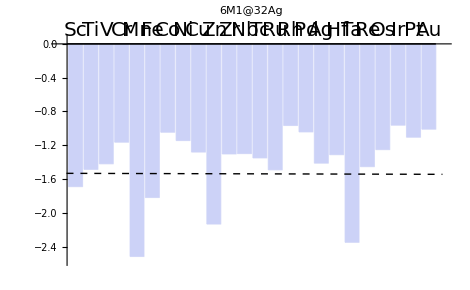
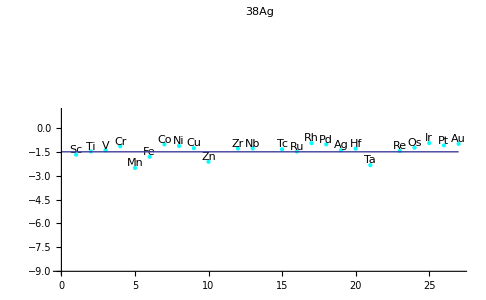
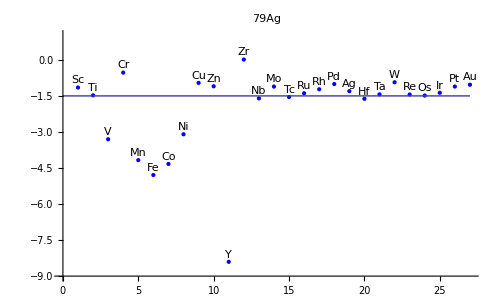
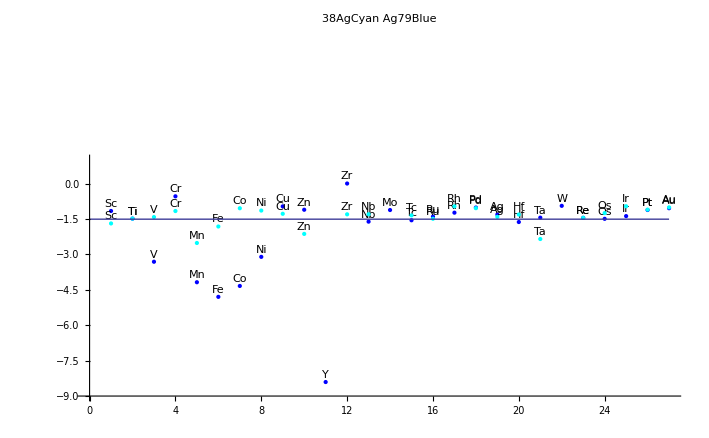
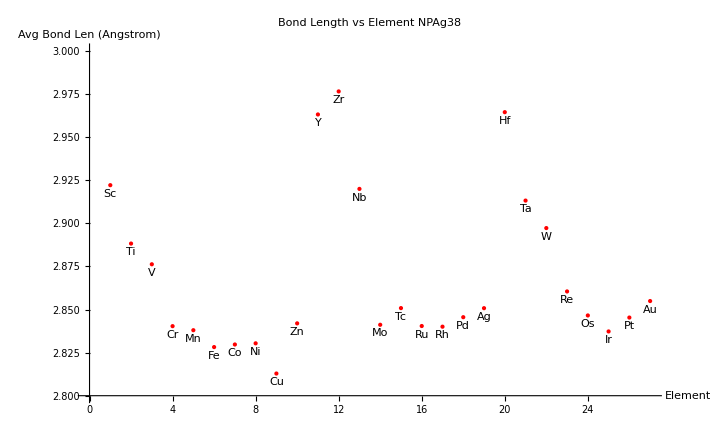
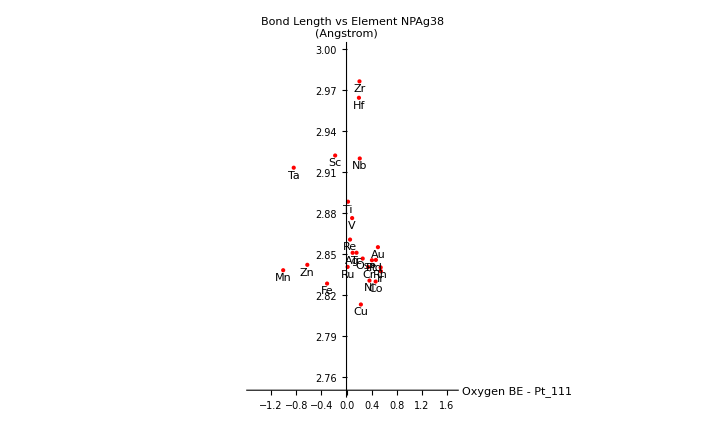
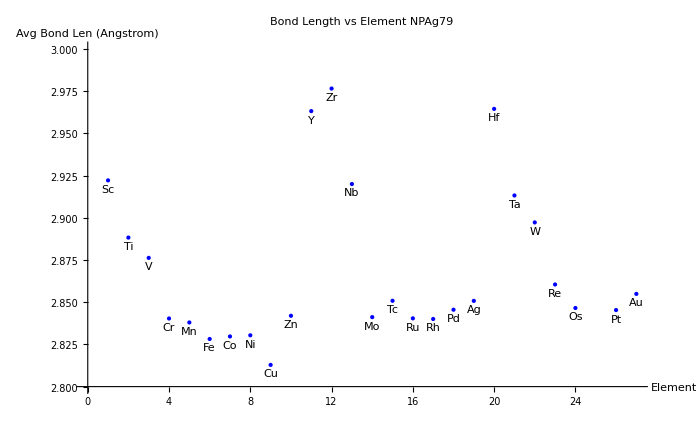
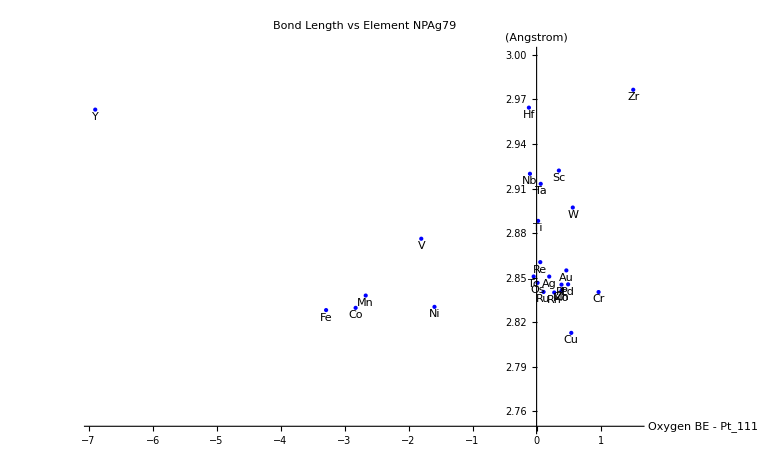
```mathematica
Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics-
```

Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics-

```mathematica
Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics-
```

Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics-

```mathematica
stackTest = {{1,2,3,4,5,6,7,8,9,10}}
```

{{1,2,3,4,5,6,7,8,9,10}}

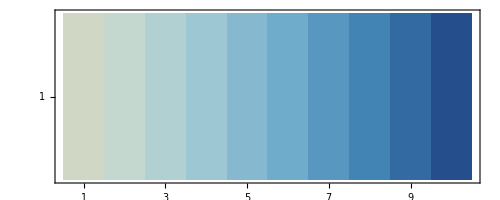

```mathematica
MatrixPlot[stackTest, ColorFunction->"RedBlueTones"]
```

```mathematica
Length[tunableORRData]
```

0

```mathematica
smallBindingTable
```

```mathematica
Function[myTable, {tunableORRData = Replace[myTable ,a_/;Abs[a]≥10->0,{2}] - ORR /. targets;d=Sign@Diagonal@tunableORRData; returnValue[row_, col_,myTable] := myTable[[row,col]] ;tunablePairs = Position[(tunableORRDataᵀ d)ᵀ,_?Negative]  /. Reverse /@ elementList; pairEnergy = returnValue[#1, #2]& @@{#1,#2}&@@@Position[(tunableORRDataᵀ d)ᵀ,_?Negative] ;
tempVar = Partition[Riffle[tunablePairs, pairEnergy],2];
filterImposs = Replace[tempVar,a_/;Abs[a]≥5->0 ,{2}] ;
filterImposs = Replace[filterImposs,a_/;a > 1->0 ,{2}] ;
Cases[filterImposs,{x_,y_}/;y ≠ 0]}][#] & /@ {smallBindingTable, bigBindingTable}








(*Cases[tt,x_/;Abs[x[[1]]-x[[2]]]>3];*)
```

{{{}},{{}}}

```mathematica
tst = { {1,2,3}, {2,3,4}, {4,5,6} }
```

{{1,2,3},{2,3,4},{4,5,6}}

```mathematica
tst[[All,1]]
tst[[All,2]]
```

{1,2,4}

{2,3,5}

```mathematica
{2,3,5}
```

{2,3,5}

```mathematica
L[#]& @@{1}
```

L[1]

```mathematica
shit = { { {a,b},1,2 }, { {l,x},2,5 } }
```

{{{a,b},1,2},{{l,x},2,5}}

```mathematica
Thread[Append, shit ,{2}]
```

Append

```mathematica
m[[1]]
```

{{a c,b l},6,3}